Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys

# Calculus 2 Lists, sets and sequences

```mathematica
List
Using braces {} and double square brackets[[]]
Drop, Take, Append, Prepend, Insert
Length,Union,Join,Intersection, Flatten,Sort
ListPlot
Table, TableForm,Range, Sum
```

## Lists

A list is an ordered collection of objects, separated by commas and enclosed by braces { }. In fact these braces are a shorthand notation for the command List[ ].
 A list is a characteristic, elementary object in Mathematica, and is widely used. For example, all kinds of data, vectors and matrices can easily be represented by lists.
Members, or elements, of a list may be of different types: all kinds of numbers, symbols, functions and even lists.
Each element of a list has its own ordering number, i.e. the number of the place in the list. You can point to a specific element in a list with the help of the number of the element in the list between double square brackets [[ ]].
Because of the ordering property a list is actually not a set, although you can use it to represent a set (see lateron). On the other hand, a list of numbers can properly be considered as a (finite) sequence.

### Examples

```mathematica
{5,7}
```

```mathematica
{3,2.3,2 a,x^2,{3,x}}
```

This is the common shorthand notation for List[ ], so the former examples could also be written as:

```mathematica
List[5,7]
```

```mathematica
List[3,2.3,2 a,x^2,{3,x}]
```

If you forget to close all braces, then you get an error message:

```mathematica
{3,2.3,2a,x^2,{3,x}
```

In order to be able to manipulate lists it is convenient to use names for lists.

```mathematica
mixlist={3,2.3,2 a,x^2,{3,x}}
```

Now we can easily point to an element of this list, e.g. the second one:

```mathematica
mixlist⟦2⟧
```

The last one is again a list:

```mathematica
mixlist⟦5⟧
```

If we want to point to the second element in this list, then we can add another argument between the double square brackets:

```mathematica
mixlist⟦5,2⟧
```

Hence, this represents the 2nd element of the 5th element of mixlist.

Remark:

The double square brackets can also be used to point to parts of arbitrary composed expressions. E.g., if we have

```mathematica
expr1=3+a
```

then we see, that this expression consists of the two parts 3 and a, separated by +. Now we can ask for the 1st or the 2nd part of this expression:

```mathematica
expr1⟦2⟧
```

Now try for yourself to point to the x of x^2 in mixlist. Remember that x^2 can also be written as x^2, so it is clear that x is the 1st part of the expression and 2 the 2nd part.

### Length

The Length command gives the number of elements in a list and turns out to be a convenient tool.

```mathematica
?Length
```

```mathematica
mixlist={3,2.3,2 a,x^2,{3,x}}
```

```mathematica
Length[mixlist]
```

```mathematica
Length[mixlist⟦5⟧]
```

## Manipulating lists

Mathematica has several tools to manipulate lists. In order to demonstrate some of these tools we define some specific lists:

```mathematica
list1={1,-4,a,{r,6},1}
list2={-4,{v,w},a}
```

If you have a long list with data (e.g. numbers or other lists), then it is easy to remove or take elements of the list with the help of the Drop and Take command.

```mathematica
?Drop
```

```mathematica
Drop[list1,2]
```

```mathematica
Drop[list1,-2]
```

```mathematica
?Take
```

```mathematica
Take[list1,2]
```

```mathematica
Take[list1,-2]
```

There are several commands to add an element to a list:

```mathematica
?Append
```

```mathematica
Append[list1,new]
```

```mathematica
?Prepend
```

```mathematica
Prepend[list1,new]
```

```mathematica
?Insert
```

```mathematica
Insert[list1,new,2]
```

```mathematica
Insert[list1,new,-2]
```

```mathematica
Insert[list1,new,{-2,3}]
```

```mathematica
Insert[list1,new,{{-2},{3}}]
```

The command Flatten skips all interior braces and yields a simple list.

```mathematica
?Flatten
```

```mathematica
Flatten[list1]
```

```mathematica
Flatten[{2,{3,{2,1}}}]
```

Or, if you only want to flatten to level one:

```mathematica
Flatten[{2,{3,{2,1}}},1]
```

Lists can be combined in different ways: Join just puts the second list after the first one, while on the other hand Union deals with lists as sets and yields the union of sets, where the elements are lexicographically ordered. 
Besides, it is possible to use Sort to order a list.

```mathematica
?Join
```

```mathematica
Join[list1,list2]
```

```mathematica
?Union
```

```mathematica
Union[list1,list2]
```

```mathematica
?Sort
```

```mathematica
Sort[list1]
```

Intersection just does what you expect it to do:

```mathematica
?Intersection
```

```mathematica
Intersection[list1,list2]
```

Remark on sets:

It is easy to simulate sets (no multiples allowed): just take Union of a list and the result can be considered as a set: each element will occur only once.

```mathematica
Union[list1]
```

## Creating a list using Table or Range

Mathematica has a very convenient tool to compose lists, generated by a function, namely the Table-command. In fact these lists are (finite) sequences. For example, if we want to have a list of the first 100 squares , then this can easily be done with the help of Table:

```mathematica
?Table
```

```mathematica
Table[n^2,{n,100}]
```

A simpler list is a list of a fixed number of identical objects:

```mathematica
Table[moon,{20}]
```

We can also ask for the squares of 50 to 100, or the squareroots of all even numbers between 1 and 100:

```mathematica
Table[n^2,{n,50,100}]
```

```mathematica
Table[√n,{n,2,100,2}]
```

If we want numerical results, just put N in front of the Table-command:

```mathematica
N[Table[√n,{n,2,100,2}]]
```

Table can also generate a list of lists, e.g. a list of lists of a number, its square, third and fourth power, from 1 to 15:

```mathematica
Table[{n,n^2,n^3,n^4},{n,1,15}]
```

In order to get a more surveyable lay-out we can use TableForm:

```mathematica
TableForm[Table[{n,n^2,n^3,n^4},{n,1,15}]]
```

This is the socalled prefix-notation, because TableForm is put in front of the Table-command. But it is also possible to put it after the Table-command (postfix-notation), preceded by double slash //

```mathematica
Table[{n,n^2,n^3,n^4},{n,1,15}]//TableForm
```

A very easy tool to create a list is the Range command:

```mathematica
?Range
```

As you see, this command generates only very simple constantly increasing, or decreasing, sequences. 
Some examples:

```mathematica
Range[10]
```

```mathematica
Range[5,10]
```

```mathematica
Range[1,3,0.01]
```

```mathematica
Range[2.1,1.5,-0.1]
```

## Plotting a list

Lists, that consist of numbers only, can easily be plotted using ListPlot.

```mathematica
?ListPlot
```

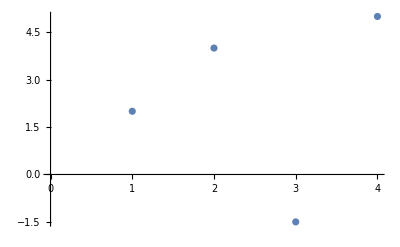

```mathematica
ListPlot[{2,4,-1.5,5}]
```

If the plotted points are too small, you can enlarge the figure by pointing and dragging with the mouse pointer.
As the following demonstrates, of course only numerical values can be plotted.

```mathematica
ListPlot[{2,4,f,-1.5,5}]
```

Notice that in the ListPlot graph the argument along the horizontal axis is just the number of the position of the corresponding number in the list. 
But also plotting points in the (2 dimensional) plane with two coordinates given is easy.

```mathematica
ListPlot[{{1,2},{2,3},{1,-3},{0,0},{1,2}}]
```

And if we join these points, we get:

```mathematica
ListPlot[{{1,2},{2,3},{1,-3},{0,0},{1,2}},Joined->True]
```

## Adding the entries of a table using Sum

Consider the list of squares from 1 to 100:

```mathematica
Table[n^2,{n,100}]
```

If we want to add all these numbers, then apply the command Sum:

```mathematica
?Sum
```

```mathematica
Sum[n^2,{n,100}]
```

More complicated sums can easily be done, for example, if we want to add all numbers n^2/3^m for n from 1 to 10 and m from 10 to 100 with stepsize 10 (so m = 10, 20, 30, ..., 100), then apply Sum as follows:

```mathematica
Sum[n^2/3^m,{n,10},{m,10,100,10}]
```

with numerical approximation:

```mathematica
N[%]
```

## Exercises

1. 	Make a "list of 4 lists of 3 lists of 2 elements", i.e. a list containing 4 elements, 
	that are itself lists of 3 lists, each consisting of 2 elements. Give this list a name 
	and point to the last element of the last list of the last list.
2. 	Use the Table-command to determine whether n^2-n+41 is a prime-number, 
	for all values of n from 1 to 60. Try to get output that is conveniently arranged 
	with the help of TableForm. (Hint: you need the PrimeQ command, find its working yourself).
3. 	Make a table of 20 random integers between -9 and 9 and plot this table.
4.	Use Manipulate to plot a table of n random integers between -9 and 9, 
	taking for n integer values between 1 and 100.
Answers

```mathematica
list1= {{{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0}}}
```

{{{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0}}}

```mathematica
list1[[4]][[3]][[2]]
```

0

```mathematica
Table[PrimeQ[n^2-n+41],n,60]
```

Table::nliter: Non-list iterator n at position 2 does not evaluate to a real numeric value.

```mathematica
TableForm[Table[PrimeQ[n^2-n+41],{n,60}]]
```

True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
False
False
True
True
False
True
True
True
True
False
True
True
True
True
True
True
False
True
True
True

```mathematica
Manipulate[ListPlot[RandomInteger[{-9,9},n]]1,100]
?Manipulate
```

Manipulate::vsform: Manipulate argument 100 does not have the correct form for a variable specification.

Manipulate[ListPlot[RandomInteger[{-9,9},n]] 1,100]

```mathematica
Manipulate[ListPlot[RandomInteger[{-9,9},n]],{n, 1,100,1}]
```

Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys